```mathematica
Quit[];
```

## Orbital Evolution modelBSK19

```mathematica
SetDirectory[NotebookDirectory[]]
Needs["NumericalCalculus`"];
consG=6.67384×10^-11;
consC=299792458.0;
MSUN=1.988409902147041*10^30;
Rns=12000;
ρc=(1.4*MSUN)/(1/4 π^2 Rns^3);
```

/media/nanoha/存储/PythonTemp/NSPBGW/code00

```mathematica
NSModel="1";
metricavaccum[r_]:=1-(2*1.4*MSUN*consG)/(r*consC^2);
prhodata=Import["model"<>NSModel<>"prho.txt","Table"];
alphadata=Import["model"<>NSModel<>"alpha.txt","Table"];
mdata=Import["model"<>NSModel<>"m.txt","Table"];
rhodata=Import["model"<>NSModel<>"rho.txt","Table"];
metrica=Interpolation[Transpose[{alphadata[[All,1]],Exp[2alphadata[[All,2]]]}]];
metricb=Interpolation[Transpose[{alphadata[[All,1]],(1-(2consG mdata[[All,2]])/(alphadata[[All,1]] consC^2))^-1}]];
dmetrica=Interpolation[Transpose[{alphadata[[All,1]],2alphadata[[All,3]]Exp[2alphadata[[All,2]]]}]];
dmetricb=Interpolation[Transpose[{alphadata[[All,1]],(2 consC^2 consG (-mdata[[All,2]]+alphadata[[All,1]] mdata[[All,3]]))/(consC^2 alphadata[[All,1]]-2 consG mdata[[All,2]])^2}]];
m=Interpolation[Transpose[{mdata[[All,1]],mdata[[All,2]]}]];
ρ=Interpolation[Transpose[{rhodata[[All,1]],rhodata[[All,2]]}]];
prho=Interpolation[Transpose[{prhodata[[All,1]]*10^3,prhodata[[All,2]]/10}]];
αaa=Interpolation[Transpose[{alphadata[[All,1]],alphadata[[All,2]]}]];
```

```mathematica
αaa[10700]
```

-0.19362137655588736

### Orbital Evolution

```mathematica
Msun=1.98847*10^30;                      (* Mass of the sun*)
Mpc=3.085677581*10^22;               (* million par second *)
pc=3.085677581*10^16;                  (* parsecond *)
ly=365*3600*24*c;                          (* light year *)
Mly=10^6*365*24*3600*c;          (* million light year *)
H0=67.9*10^3/Mpc;                    (* Hubble constant *)
c=299792458;                                 (* Speed of light *)
Gn=6.67408*10^-11;(* Gravitational constant *)    
ρs=7.86*10^3;(*ρFe=7.86*10^3 kg/m^3*)
mn=1.4Msun; 
yt=365*3600*24;(* the NS parameters*)
```

```mathematica
βa[r_]:=1/2 Log[(1-(2Gn m[r])/(r c^2))^-1];
Ba[r_]:=(1-(2Gn m[r])/(r c^2))^-1;
dαadr[r_]:=(Gn (m[r]+4π r^3 prho[ρ[r]]/c^2))/(r^2 c^2(1-2Gn m[r]/(r c^2)));
ddαaddr[r_]:=Evaluate[D[dαadr[r],r]];
dBadr[r_]:=Evaluate[D[Ba[r],r]];
Aa:=metrica;
```

-Graphics-

-Graphics-

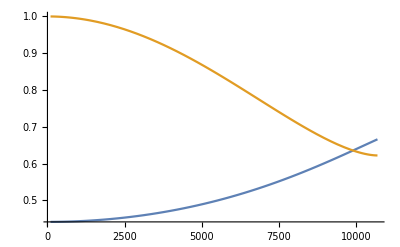

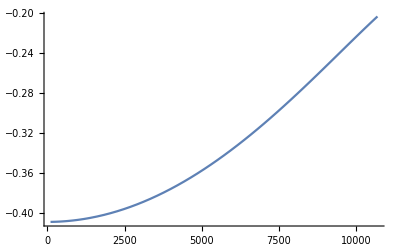

```mathematica
Plot[ρ[r],{r,100,10000}]
Plot[prho[ρ[r]],{r,100,10000}]
Plot[{metrica[r],1/metricb[r]},{r,100,10700}]
Plot[αaa[r],{r,100,10700}]
```

```mathematica
(*cs1[r_]=(dpadρ[ρ1[r]])^(1/2);*)
csa[r_]=√prho'[ρ[r]];
ωa[r_]=c(dαadr[r] metrica[r]/r)^(1/2);
va[r_]=ωa[r]r;
calMa[r_]=va[r]/ csa[r];
```

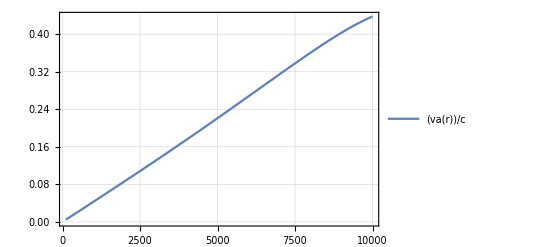

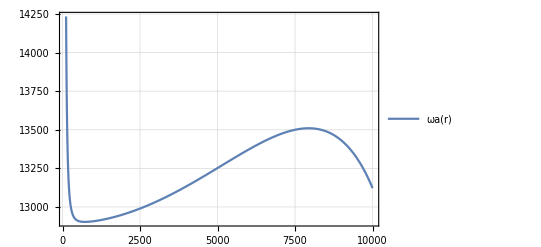

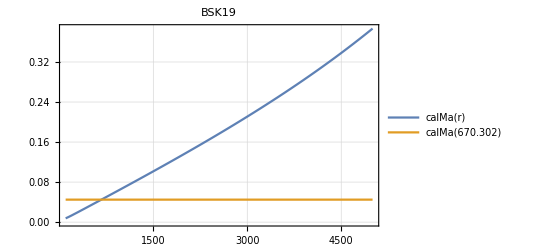

```mathematica
Plot[va[r]/c,{r,100,10000},PlotTheme->"Detailed"]
Plot[ωa[r],{r,100,10000},PlotTheme->"Detailed"]
Plot[{calMa[r],calMa[670.3017]},{r,100,5000},PlotTheme->"Detailed",PlotLabel->"BSK19"]
```

```mathematica
Iϕa[r_]=Piecewise[{{calMa[r]^3/3-0.80352calMa[r]^4+7.68585calMa[r]^5,0<calMa[r]<0.08588},{0.7706Log[(1+calMa[r])/(1.0004-0.9185calMa[r])]-1.4703calMa[r],0.08588<calMa[r]<1.0},{Log[3300(calMa[r]-0.71)^5.72 calMa[r]^-9.58],1.0<=calMa[r]<4.4},{Log[10/(0.11calMa[r]+1.65)],4.4<=calMa[r]}}];
Ira[r_]=Piecewise[{{calMa[r]^2 10^(3.51calMa[r]-4.22),calMa[r]<1.1},{0.5Log[9.33 calMa[r]^2(calMa[r]^2-0.95)],1.1<=calMa[r]<4.4},{0.3 calMa[r]^2,4.4<=calMa[r]}}];
fra1[t_]=(*-(M*m[r])/(Mcs*r^2)*)(-4π ρ[r[t]] Gn^2 mp[t]^2/va[r[t]]^2)Iϕa[r[t]];
fra2[t_]=(*-(M*m[r])/(Mcs*r^2)*)(-4π ρ[r[t]] Gn^2 1/va[r[t]]^2)Ira[r[t]]mp[t]/c^2;(*fr2/mp in geometirc *)
dfr2dra[t_]=Evaluate[D[(-4π ρ[r[t]] Gn^2 1/va[r[t]]^2)Ira[r[t]],r[t]]]mp[t]/c^2+(-4π ρ[r[t]] Gn^2 1/va[r[t]]^2)Ira[r[t]]mp'[t]/(c^2 r'[t]);
```

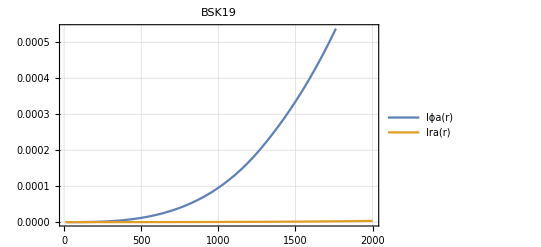

```mathematica
Plot[{Iϕa[r],Ira[r]},{r,10,2000},PlotTheme->"Detailed",PlotLabel->"BSK19"]
```

```mathematica
orbEa2[r_]=√((Aa[r](Ba[r]fra2[r]r-1))/(r dαadr[r]-1))c^2;
orbEta2[t_]=√((Aa[r[t]](Ba[r[t]]fra2[t]r[t]-1))/(r[t] dαadr[r[t]]-1))c^2;
doEdta2[t_]=(( (3  dαadr[r[t]]-2 r[t]  dαadr[r[t]]^2+r[t]  ddαaddr[r[t]])/(2(1- r[t] dαadr[r[t]])))√((Aa[r[t]](1-r[t] Ba[r[t]] fra2[t]))/(1-r[t] dαadr[r[t]]))-1/2(r[t] fra2[t] dBadr[r[t]]+ fra2[t]Ba[r[t]]+r[t]dfr2dra[t]Ba[r[t]])√(Aa[r[t]]/((1-r[t] Ba[r[t]] fra2[t])(1-r[t] dαadr[r[t]]))))r'[t] c^2;
doEdra2[t_]=(( (3  dαadr[r[t]]-2 r[t]  dαadr[r[t]]^2+r[t]  ddαaddr[r[t]])/(2(1- r[t] dαadr[r[t]])))√((Aa[r[t]](1-r[t] Ba[r[t]] fra2[t]))/(1-r[t] dαadr[r[t]]))-1/2(r[t] fra2[t] dBadr[r[t]]+ fra2[t]Ba[r[t]](*+r[t]dfr2dt[t]B1[r[t]]*))√(Aa[r[t]]/((1-r[t] Ba[r[t]] fra2[t])(1-r[t] dαadr[r[t]]))))c^2;
```

```mathematica
λa=0.707;
dmpdta[t_]=4π λa ρ[r[t]](Gn^2 mp[t]^2)/((csa[r[t]]^2+va[r[t]]^2)^(3/2));
adϵdtgfa[t_]=(dmpdta[t]/mp[t])√(Aa[r[t]]-r[t] Aa[r[t]]dαadr[r[t]])c^2;
(*adϵdtgfa[t_]=-4π λa ρ[r[t]](Gn^2 mp[t])/((csa[r[t]]^2+va[r[t]]^2)^(3/2)) va[r[t]]^2;*)
adϵdtgdf[t_]=(-4π ρ[r[t]] Gn^2 mp[t]/va[r[t]]^2)Iϕa[r[t]]va[r[t]];
agwdϵdt[t_]=(-(32Gn r[t]^4 mp[t] ωa[r[t]]^6)/(5 c^5)+1/(5 c^7)2Gn r[t]^4 mp[t] ωa[r[t]]^6(-16 r[t]^2 ωa[r[t]]^2+(16+24(Aa[r[t]]-Ba[r[t]])^2)(1-Aa[r[t]])/2)-(8Gn r[t]^6 mp[t] ωa[r[t]]^8)/(45 c^7)-(2734Gn r[t]^6 mp[t] ωa[r[t]]^8)/(315 c^7))-(4π λa ρ[r[t]])^2(Gn^4 mp[t]^3)/((csa[r[t]]^2+va[r[t]]^2)^3)((72Gn r[t]^4 ωa[r[t]]^4)/(5 c^5)+(4864Gn r[t]^6 ωa[r[t]]^6)/(315 c^7)+(8Gn r[t]^6 ωa[r[t]]^6)/(5 c^7));
dphidt[t_]:=c*Sqrt[dmetrica[r[t]]/(2*r[t])];
omega[r_]:=c*Sqrt[dmetrica[r]/(2*r)];
```

## Evolution

```mathematica
Endtimes={81.7,101.7}
tmax=Endtimes[[NSModel+1]]
```

```mathematica
(* dE=μdϵ+ϵdμ *)
mpini=10^-6 Msun;
BSH=NDSolve[{mp'[t]==dmpdta[t],r'[t]==(adϵdtgfa[t]+adϵdtgdf[t]+agwdϵdt[t]-(dmpdta[t]/mp[t])orbEta2[t])/(doEdra2[t]),phi'[t]==dphidt[t],r[0]==10000,mp[0]==mpini,phi[0]==0},{mp,r,phi},{t,0,102},MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]
mpRes[t_]=mp[t]/.Flatten[BSH];
rRes[t_]=r[t]/.Flatten[BSH];
phiRes[t_]:=phi[t]/.Flatten[BSH];
tend=t/.FindRoot[mpRes[t]/Msun==0.01,{t,10}]
mpRes[tend]/Msun
Export[ "Mm6_orbit_model"<>NSModel<>".txt", Table[N[{t,rRes[t],mpRes[t],phiRes[t],omega[rRes[t]]},16],{t,0,tend,0.1}],"Table"]
```

NDSolve::ndsz: 在 t == 101.701 处，步长实际上为零；可能存在奇点或者刚性系统.

{{mp→InterpolatingFunction[…],r→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: 输入值 {120.} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {241.} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {483.} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

101.701

0.01

Mm6_orbit_model1.txt

```mathematica
(* dE=μdϵ+ϵdμ *)
mpini=10^-5 Msun;
BSH=NDSolve[{mp'[t]==dmpdta[t],r'[t]==(adϵdtgfa[t]+adϵdtgdf[t]+agwdϵdt[t]-(dmpdta[t]/mp[t])orbEta2[t])/(doEdra2[t]),phi'[t]==dphidt[t],r[0]==10000,mp[0]==mpini,phi[0]==0},{mp,r,phi},{t,0,tmax/10},MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]
mpRes[t_]=mp[t]/.Flatten[BSH];
rRes[t_]=r[t]/.Flatten[BSH];
phiRes[t_]:=phi[t]/.Flatten[BSH];
tend=t/.FindRoot[mpRes[t]/Msun==0.01,{t,10}]
mpRes[tend]/Msun
Export[ "Mm5_orbit_model"<>NSModel<>".txt", Table[N[{t,rRes[t],mpRes[t],phiRes[t],omega[rRes[t]]},16],{t,0,tend,0.1}],"Table"]
```

{{mp→InterpolatingFunction[…],r→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: 输入值 {10.} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {84.9169} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {17.4917} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

19.1836

InterpolatingFunction::dmval: 输入值 {19.1836} 位于插值函数的数据范围之外. 将使用外推法.

0.01

InterpolatingFunction::dmval: 输入值 {8.2} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

Mm5_orbit_model1.txt

```mathematica
(* dE=μdϵ+ϵdμ *)
mpini=10^-4 Msun;
BSH=NDSolve[{mp'[t]==dmpdta[t],r'[t]==(adϵdtgfa[t]+adϵdtgdf[t]+agwdϵdt[t]-(dmpdta[t]/mp[t])orbEta2[t])/(doEdra2[t]),phi'[t]==dphidt[t],r[0]==10000,mp[0]==mpini,phi[0]==0},{mp,r,phi},{t,0,tmax/100},MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]
mpRes[t_]=mp[t]/.Flatten[BSH];
rRes[t_]=r[t]/.Flatten[BSH];
phiRes[t_]:=phi[t]/.Flatten[BSH];
tend=t/.FindRoot[mpRes[t]/Msun==0.01,{t,10}]
mpRes[tend]/Msun
Export[ "Mm4_orbit_model"<>NSModel<>".txt", Table[N[{t,rRes[t],mpRes[t],phiRes[t],omega[rRes[t]]},16],{t,0,tend,0.1}],"Table"]
```

{{mp→InterpolatingFunction[…],r→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: 输入值 {10.} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {6.91669} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {4.86159} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

1.27332

InterpolatingFunction::dmval: 输入值 {1.27332} 位于插值函数的数据范围之外. 将使用外推法.

0.01

InterpolatingFunction::dmval: 输入值 {0.9} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

Mm4_orbit_model1.txt

```mathematica
(* dE=μdϵ+ϵdμ *)
mpini=10^-3 Msun;
BSH=NDSolve[{mp'[t]==dmpdta[t],r'[t]==(adϵdtgfa[t]+adϵdtgdf[t]+agwdϵdt[t]-(dmpdta[t]/mp[t])orbEta2[t])/(doEdra2[t]),phi'[t]==dphidt[t],r[0]==10000,mp[0]==mpini,phi[0]==0},{mp,r,phi},{t,0,tmax/1000},MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]
mpRes[t_]=mp[t]/.Flatten[BSH];
rRes[t_]=r[t]/.Flatten[BSH];
phiRes[t_]:=phi[t]/.Flatten[BSH];
tend=t/.FindRoot[mpRes[t]/Msun==0.01,{t,10}]
mpRes[tend]/Msun
Export[ "Mm3_orbit_model"<>NSModel<>".txt", Table[N[{t,rRes[t],mpRes[t],phiRes[t],omega[rRes[t]]},16],{t,0,tend,0.1}],"Table"]
```

{{mp→InterpolatingFunction[…],r→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: 输入值 {10.} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {6.69165} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {4.48609} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

0.0927909

InterpolatingFunction::dmval: 输入值 {0.0927909} 位于插值函数的数据范围之外. 将使用外推法.

0.01

Mm3_orbit_model1.txt